## Higgs inclusive

## Parameters

```mathematica
(* Small N contributions *)
c10 = 2.28;
c20 = 4.12;
c30 = 8.64;
c11 = 5.66;
c21 = 10.54;
(* Large N contributions*)
g01old = 8.7153;
g02 = 40.10;
g12 = 2 ca / π;
g21 = 2 ca EulerGamma / π;
(* Analytic g01 - double check *)
g01 = 2/π(3 EulerGamma^2 + π^2 + 11/4);
```

```mathematica
N@g01
```

8.67021

## Mellin transformation

```mathematica
(* Shift N to match results in Stefano's paper *)
(* Mellin integral over z^(N-2) to have the right-most pole at N = 1*)
```

```mathematica
mymellin1 = Integrate[Log[1-z]/(1-z)*(z^(n-2)(1-z+z^2)^2 - 1),{z,0,1},Assumptions->{Re[n]>1}]
```

1/(12 (-1+n) n^2 (1+n)^2 (2+n)^2)(-96-72 n-96 EulerGamma n+264 n^2-168 EulerGamma n^2-24 EulerGamma^2 n^2+396 n^3-12 EulerGamma n^3-48 EulerGamma^2 n^3+240 n^4+144 EulerGamma n^4-6 EulerGamma^2 n^4+60 n^5+108 EulerGamma n^5+42 EulerGamma^2 n^5+24 EulerGamma n^6+30 EulerGamma^2 n^6+6 EulerGamma^2 n^7-4 n^2 π^2-8 n^3 π^2-n^4 π^2+7 n^5 π^2+5 n^6 π^2+n^7 π^2+12 n (-2-n+2 n^2+n^3) (4+(5+2 EulerGamma) n+(2+3 EulerGamma) n^2+EulerGamma n^3) PolyGamma[0,-1+n]+6 (-1+n) n^2 (2+3 n+n^2)^2 PolyGamma[0,-1+n]^2-6 (-1+n) n^2 (2+3 n+n^2)^2 PolyGamma[1,-1+n])

```mathematica
mymellin2 = Integrate[z^(n-2)*(1-z+z^2)^2*Log[z]/(1-z),{z,0,1},Assumptions->{Re[n]>1}]
```

2/n^2-1/(1+n)^2+1/(2+n)^2-PolyGamma[1,-1+n]

```mathematica
mymellin3 = Integrate[z^(n-2)(1-z)^3,{z,0,1},Assumptions->{Re[n]>1}] (* this is Rgg approx*)
```

6/(n (-2-n+2 n^2+n^3))

```mathematica
mymellin4 = Integrate[z^(n-2) DiracDelta[1-z],{z,0,1},Assumptions->{Re[n]>0}]
```

HeavisideTheta[0]

```mathematica
mymellin = ca/π(4 mymellin1 - 2 mymellin2 - 11/6 mymellin3 + (2Zeta[2] + 11/6))
```

1/π ca (11/6-11/(n (-2-n+2 n^2+n^3))+π^2/3-2 (2/n^2-1/(1+n)^2+1/(2+n)^2-PolyGamma[1,-1+n])+1/(3 (-1+n) n^2 (1+n)^2 (2+n)^2)(-96-72 n-96 EulerGamma n+264 n^2-168 EulerGamma n^2-24 EulerGamma^2 n^2+396 n^3-12 EulerGamma n^3-48 EulerGamma^2 n^3+240 n^4+144 EulerGamma n^4-6 EulerGamma^2 n^4+60 n^5+108 EulerGamma n^5+42 EulerGamma^2 n^5+24 EulerGamma n^6+30 EulerGamma^2 n^6+6 EulerGamma^2 n^7-4 n^2 π^2-8 n^3 π^2-n^4 π^2+7 n^5 π^2+5 n^6 π^2+n^7 π^2+12 n (-2-n+2 n^2+n^3) (4+(5+2 EulerGamma) n+(2+3 EulerGamma) n^2+EulerGamma n^3) PolyGamma[0,-1+n]+6 (-1+n) n^2 (2+3 n+n^2)^2 PolyGamma[0,-1+n]^2-6 (-1+n) n^2 (2+3 n+n^2)^2 PolyGamma[1,-1+n]))

```mathematica
(* Numerical values *)
αs = 0.118;
nf = 5;
ca = 3;
cf = 4 / 3;
β0 = (33 - 2 nf) / 3;
```

```mathematica
(* Prepare exact FO cross section *)
tableExact = Table[{n, mymellin}, {n, 1.3,12.01, 0.01}];
Nexact = tableExact[[All, 1]];
SigmaNexact = tableExact[[All, 2]];
```

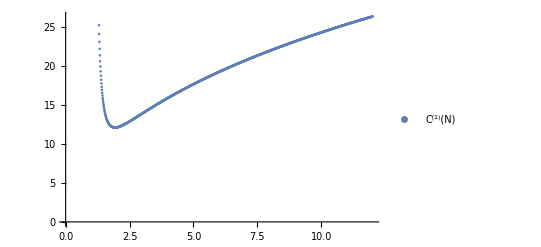

```mathematica
ListPlot[{tableExact}, PlotLegends -> {"C^(1)(N)"}] (* 2.12 *)
```

## Asymptotics - Small N

```mathematica
(* Clear numerical values *)
Clear[αs, ca, cf, β0]
```

```mathematica
(* Constants in (2.51) & (2.52) *)
e00 = (-11 ca + 2nf (2  cf/ca -1))/(12 π);
e01 = ca / π;
e11 = ((13 cf)/(18 π) - (23 ca)/(36 π)) nf;
e12 = 0;
e22 = (ca^3 Zeta[3])/(2 π^3) + (11 ca^3 Zeta[2])/(12 π^3) - (395 ca^3)/(108 π^3) + ((ca^2 Zeta[2])/(6 π^3) - (71 ca^2)/(108 π^3) - (cf ca Zeta[2])/(3 π^3) + (71 cf ca)/(54 π^3)) nf;
e23 = 0;
γ0 = e01/(n - 1) + e00;
γ1 = e12/(n - 1)^2 + e11/(n - 1);
γ2 = e23/(n - 1)^3 + e22/(n - 1)^2;
(* Result (2.53) and subleading version (2.54) *)
mellinNsmall = 2 c10 γ0 (*αs + αs^2((2 c20 + c11) γ0^2 - 2 c20 β0 γ0 + 2 c10 γ1) + αs^3((c30 + c11)2 γ0^3 - (3 c30 + c21)2 β0 γ0^2 + 4 c30 β0^2 γ0 + (2 c20 + c11)2 γ0 γ1 - 4 c20 β0 γ1 + 2 c10 γ2)*)
mellinNsmall2 = mellinNsmall + (mellinNsmall /. n  -> n +1 ) + (mellinNsmall /. n  -> n +2 )
```

4.56 ((-11 ca+10 (-1+(2 cf)/ca))/(12 π)+ca/((-1+n) π))

4.56 ((-11 ca+10 (-1+(2 cf)/ca))/(12 π)+ca/((-1+n) π))+4.56 ((-11 ca+10 (-1+(2 cf)/ca))/(12 π)+ca/(n π))+4.56 ((-11 ca+10 (-1+(2 cf)/ca))/(12 π)+ca/((1+n) π))

```mathematica
(* Numerical values *)
αs = 0.118;
nf = 5;
ca = 3;
cf = 4 / 3;
β0 = (33 - 2 nf) / 3;
```

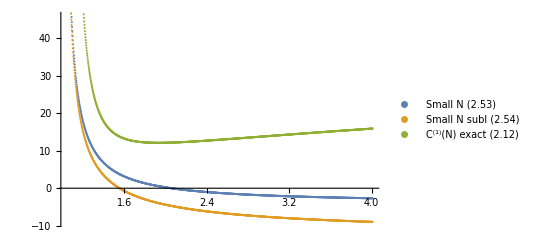

```mathematica
tableNsmallTest = Table[{n, mellinNsmall}, {n, 1.03, 4.01, 0.0025}];
tableNsmallTest2 = Table[{n, mellinNsmall2} , {n, 1.03, 4.01, 0.0025}];
tableExactTestSmall = Table[{n, mymellin}, {n, 1.03, 4.01, 0.0025}];
ListPlot[{tableNsmallTest, tableNsmallTest2, tableExactTestSmall}, PlotLegends -> {"Small N (2.53)", "Small N subl (2.54)", "C^(1)(N) exact (2.12)"}]
```

```mathematica
(* Check poles *)
Series[mymellin,{n,1,0}]
Series[mellinNsmall,{n,1,0}]
```

6/(π (n-1)^2)-11/(2 π (n-1))+107/(4 π)+O[n-1]^1

4.35448/(n-1)-4.126+O[n-1]^1

## Asymptotics - Large N

```mathematica
(* Clear numerical values *)
Clear[αs, ca, cf, β0]
```

```mathematica
(* Appendix A.1 *)
dΓ[k_][n_]:=Module[{m},D[Gamma[m],{m,k}]/.{m->n}];
dΔ[k_][n_]:=Module[{m},D[1/Gamma[m],{m,k}]/.{m->n}];
dΥ[k_][n_]:=Module[{x,e},e=D[Gamma[n-x/2]/Gamma[n+x/2],{x,k}]; e/.{x->0}];
getD[k_][n_]:=1/(k+1)Sum[Binomial[k+1,j]dΓ[j][1](Gamma[n]dΔ[k+1-j][n]-dΔ[k+1-j][1]),{j,0,k}];
getDlog[k_][n_]:=1/(k+1)Sum[Binomial[k+1,j]dΓ[j][1](-Log[n])^(k+1-j),{j,0,k}];
getDhat[k_][n_]:=1/(k+1)Sum[Binomial[k+1,j]dΓ[j][1](dΥ[k+1-j][n]-dΔ[k+1-j][1]),{j,0,k}]
```

```mathematica
(* Results (2.16), (2.2.27) and (2.28) *)
Dlog = 1/2(Log[n]^2 + 2 EulerGamma Log[n]);
Dhat = 1/2(PolyGamma[0, n]^2+ 2 EulerGamma PolyGamma[n] + Zeta[2] + EulerGamma^2);
(* Check expressions *)
Dlog-getDlog[1][n]//FullSimplify
Dhat-getDhat[1][n]//FullSimplify
```

0

0

```mathematica
Do[Print[k," = ",FullSimplify[dΓ[k+1][1]/(k+1)]],{k,0,3}]
```

0 = -EulerGamma

1 = 1/12 (6 EulerGamma^2+π^2)

2 = 1/6 (-2 EulerGamma^3-EulerGamma π^2-4 Zeta[3])

3 = 1/4 (EulerGamma^4+EulerGamma^2 π^2+(3 π^4)/20+8 EulerGamma Zeta[3])

```mathematica
(* Check Dhat expressions from appendix A.6a *)
getD[0][n] // FullSimplify
getD[1][n] // FullSimplify
getD[2][n] // FullSimplify
getD[3][n] // FullSimplify
```

-HarmonicNumber[-1+n]

1/12 (6 EulerGamma^2+π^2+6 PolyGamma[0,n] (2 EulerGamma+PolyGamma[0,n])-6 PolyGamma[1,n])

1/6 (-2 EulerGamma^3-EulerGamma π^2-PolyGamma[0,n] (6 EulerGamma^2+π^2+2 PolyGamma[0,n] (3 EulerGamma+PolyGamma[0,n]))+6 (EulerGamma+PolyGamma[0,n]) PolyGamma[1,n]-2 PolyGamma[2,n]-4 Zeta[3])

1/80 (20 EulerGamma^4+20 EulerGamma^2 π^2+3 π^4-20 PolyGamma[3,n]+20 (4 EulerGamma PolyGamma[0,n]^3+PolyGamma[0,n]^4+PolyGamma[0,n]^2 (6 EulerGamma^2+π^2-6 PolyGamma[1,n])-(6 EulerGamma^2+π^2) PolyGamma[1,n]+3 PolyGamma[1,n]^2+4 EulerGamma (PolyGamma[2,n]+2 Zeta[3])+2 PolyGamma[0,n] (2 EulerGamma^3+EulerGamma π^2-6 EulerGamma PolyGamma[1,n]+2 PolyGamma[2,n]+4 Zeta[3])))

```mathematica
(* Check Dhat expressions from appendix A.6b *)
getDlog[0][n] // FullSimplify
getDlog[1][n] // FullSimplify
getDlog[2][n] // FullSimplify
getDlog[3][n] // FullSimplify
```

-Log[n]

1/2 Log[n] (2 EulerGamma+Log[n])

-1/6 Log[n] (6 EulerGamma^2+π^2+2 Log[n] (3 EulerGamma+Log[n]))

1/4 Log[n] ((2 EulerGamma+Log[n]) (2 EulerGamma^2+π^2+2 EulerGamma Log[n]+Log[n]^2)+8 Zeta[3])

```mathematica
(* Check Dhat expressions from appendix A.6c *)
getDhat[0][n] // FullSimplify
getDhat[1][n] // FullSimplify
getDhat[2][n] // FullSimplify
getDhat[3][n] // FullSimplify
```

-HarmonicNumber[-1+n]

1/12 (π^2+6 (EulerGamma+PolyGamma[0,n])^2)

1/12 (-PolyGamma[2,n]-2 (π^2 (EulerGamma+PolyGamma[0,n])+2 (EulerGamma+PolyGamma[0,n])^3+4 Zeta[3]))

1/80 (20 EulerGamma^4+20 EulerGamma^2 π^2+3 π^4+20 ((6 EulerGamma^2+π^2) PolyGamma[0,n]^2+4 EulerGamma PolyGamma[0,n]^3+PolyGamma[0,n]^4+EulerGamma (PolyGamma[2,n]+8 Zeta[3])+PolyGamma[0,n] (4 EulerGamma^3+2 EulerGamma π^2+PolyGamma[2,n]+8 Zeta[3])))

```mathematica
(* Asymptotics at large N *)
(* Results (2.16), (2.19), (2.27) and (2.28) *)
mellinNlarge = g12 Log[n]^2 + g21 Log[n] + g01// Expand (* 2.16 *)
mellinNlarge2 = 4 ca/π Dlog+ g01 // Expand (* 2.19 *)
mellinNlarge3 = 2 g12 Dhat + g01 + (-6 (EulerGamma/π)^2- π) // Expand (* 2.28 *)
```

11/(2 π)+(6 EulerGamma^2)/π+2 π+(2 ca EulerGamma Log[n])/π+(2 ca Log[n]^2)/π

11/(2 π)+(6 EulerGamma^2)/π+2 π+(4 ca EulerGamma Log[n])/π+(2 ca Log[n]^2)/π

-(6 EulerGamma^2)/π^2+11/(2 π)+(6 EulerGamma^2)/π+(2 ca EulerGamma^2)/π+π+(ca π)/3+(4 ca EulerGamma PolyGamma[0,n])/π+(2 ca PolyGamma[0,n]^2)/π

```mathematica
(* Numerical values *)
αs = 0.118;
nf = 5;
ca = 3;
cf = 4 / 3;
β0 = (33 - 2 nf) / 3;
```

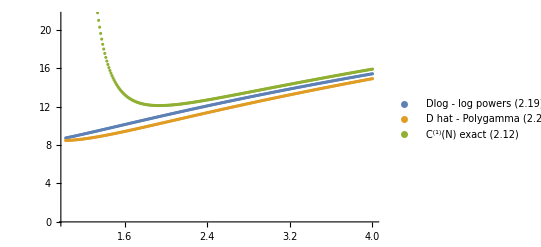

```mathematica
tableNlargeTest = Table[{n, mellinNlarge}, {n, 1.025,4.01, 0.01}];
tableNlargeTest2 = Table[{n, mellinNlarge2}, {n, 1.025,4.01, 0.01}];
tableNlargeTest3 = Table[{n, mellinNlarge3}, {n, 1.025,4.01, 0.01}];
tableExactTest = Table[{n, mymellin}, {n, 1.025,4.01, 0.01}];
ListPlot[{tableNlargeTest2,tableNlargeTest3,  tableExactTest}, PlotLegends -> {"Dlog - log powers (2.19)", "D hat - Polygamma (2.28)", "C^(1)(N) exact (2.12)"}]
```

```mathematica
(* Compute ratio *)
ratioNlarge = mellinNlarge3 / mymellin;
tableRatioNlarge = Table[ratioNlarge, {n, 15.0, 20.0, 0.1}]
```

{0.988678,0.988816,0.988953,0.989088,0.989221,0.989353,0.989482,0.98961,0.989737,0.989861,0.989984,0.990106,0.990226,0.990344,0.990461,0.990576,0.99069,0.990803,0.990914,0.991023,0.991132,0.991239,0.991345,0.991449,0.991552,0.991654,0.991755,0.991854,0.991953,0.99205,0.992146,0.992241,0.992335,0.992427,0.992519,0.99261,0.992699,0.992788,0.992875,0.992962,0.993047,0.993132,0.993216,0.993299,0.99338,0.993461,0.993541,0.993621,0.993699,0.993776,0.993853}

## Prepare GP regression

```mathematica
(* Prepare datafiles for GP regression *)
Clear[tableExact, tableNsmall, tableNlarge]
(* Numerical values *)
αs = 0.118;
nf = 5;
ca = 3;
cf = 4 / 3;
β0 = (33 - 2 nf) / 3;
```

```mathematica
(* Prepare exact FO cross section *)
tableExact = Table[{n, mymellin}, {n, 1.05, 12, 0.005}];
Nexact = tableExact[[All, 1]];
Export["~/Desktop/N3PDF/N3PDFrep/crystalball/data/N_exact_long.txt",%];
SigmaNexact = tableExact[[All, 2]];
Export["~/Desktop/N3PDF/N3PDFrep/crystalball/data/sigma_N_exact_long.txt",%];

(* Prepare asymptotics - small N *)
tableNsmall = Table[{n, mellinNsmall2}, {n, 1.05, 1.55, 0.05}];
Nsmall = tableNsmall[[All, 1]]
Export["~/Desktop/N3PDF/N3PDFrep/crystalball/data/N_small2_long.txt",%];
SigmaNsmall = tableNsmall[[All, 2]]
Export["~/Desktop/N3PDF/N3PDFrep/crystalball/data/sigma_N_small2_long.txt",%];

(* Prepare asymptotics - large N *)
tableNlarge = Table[{n, mellinNlarge3}, {n, 2.15, 12, 0.05}];
Nlarge = tableNlarge[[All, 1]]
Export["~/Desktop/N3PDF/N3PDFrep/crystalball/data/N_large2_long.txt",%];
SigmaNlarge = tableNlarge[[All, 2]]
Export["~/Desktop/N3PDF/N3PDFrep/crystalball/data/sigma_N_large2_long.txt",%];
```

{1.05,1.1,1.15,1.2,1.25,1.3,1.35,1.4,1.45,1.5,1.55}

{80.9828,37.199,22.4637,15.0024,10.4588,7.37977,5.14187,3.4329,2.07904,0.975726,0.0562049}

{2.15,2.2,2.25,2.3,2.35,2.4,2.45,2.5,2.55,2.6,2.65,2.7,2.75,2.8,2.85,2.9,2.95,3.,3.05,3.1,3.15,3.2,3.25,3.3,3.35,3.4,3.45,3.5,3.55,3.6,3.65,3.7,3.75,3.8,3.85,3.9,3.95,4.,4.05,4.1,4.15,4.2,4.25,4.3,4.35,4.4,4.45,4.5,4.55,4.6,4.65,4.7,4.75,4.8,4.85,4.9,4.95,5.,5.05,5.1,5.15,5.2,5.25,5.3,5.35,5.4,5.45,5.5,5.55,5.6,5.65,5.7,5.75,5.8,5.85,5.9,5.95,6.,6.05,6.1,6.15,6.2,6.25,6.3,6.35,6.4,6.45,6.5,6.55,6.6,6.65,6.7,6.75,6.8,6.85,6.9,6.95,7.,7.05,7.1,7.15,7.2,7.25,7.3,7.35,7.4,7.45,7.5,7.55,7.6,7.65,7.7,7.75,7.8,7.85,7.9,7.95,8.,8.05,8.1,8.15,8.2,8.25,8.3,8.35,8.4,8.45,8.5,8.55,8.6,8.65,8.7,8.75,8.8,8.85,8.9,8.95,9.,9.05,9.1,9.15,9.2,9.25,9.3,9.35,9.4,9.45,9.5,9.55,9.6,9.65,9.7,9.75,9.8,9.85,9.9,9.95,10.,10.05,10.1,10.15,10.2,10.25,10.3,10.35,10.4,10.45,10.5,10.55,10.6,10.65,10.7,10.75,10.8,10.85,10.9,10.95,11.,11.05,11.1,11.15,11.2,11.25,11.3,11.35,11.4,11.45,11.5,11.55,11.6,11.65,11.7,11.75,11.8,11.85,11.9,11.95,12.}

{10.747,10.8699,10.9924,11.1146,11.2364,11.3576,11.4784,11.5986,11.7182,11.8372,11.9555,12.0732,12.1903,12.3066,12.4222,12.5371,12.6513,12.7648,12.8776,12.9897,13.101,13.2117,13.3216,13.4308,13.5392,13.647,13.7541,13.8604,13.9661,14.0711,14.1754,14.279,14.382,14.4843,14.5859,14.6869,14.7872,14.8869,14.986,15.0844,15.1822,15.2794,15.376,15.472,15.5675,15.6623,15.7565,15.8502,15.9433,16.0359,16.1279,16.2193,16.3103,16.4007,16.4905,16.5798,16.6687,16.757,16.8448,16.9321,17.0189,17.1053,17.1911,17.2765,17.3614,17.4459,17.5299,17.6134,17.6965,17.7791,17.8613,17.9431,18.0245,18.1054,18.1859,18.266,18.3457,18.4249,18.5038,18.5823,18.6604,18.7381,18.8154,18.8923,18.9689,19.045,19.1209,19.1963,19.2714,19.3461,19.4205,19.4945,19.5682,19.6416,19.7146,19.7872,19.8596,19.9316,20.0033,20.0746,20.1457,20.2164,20.2868,20.3569,20.4267,20.4962,20.5654,20.6343,20.7029,20.7712,20.8392,20.907,20.9744,21.0416,21.1085,21.1751,21.2414,21.3075,21.3733,21.4388,21.5041,21.5691,21.6338,21.6983,21.7625,21.8265,21.8902,21.9537,22.0169,22.0799,22.1427,22.2052,22.2675,22.3295,22.3913,22.4529,22.5142,22.5753,22.6362,22.6969,22.7573,22.8175,22.8775,22.9373,22.9969,23.0562,23.1154,23.1743,23.233,23.2915,23.3498,23.4079,23.4658,23.5235,23.581,23.6384,23.6955,23.7524,23.8091,23.8656,23.922,23.9781,24.0341,24.0899,24.1455,24.2009,24.2561,24.3112,24.3661,24.4208,24.4753,24.5296,24.5838,24.6378,24.6916,24.7453,24.7988,24.8521,24.9052,24.9582,25.011,25.0637,25.1162,25.1685,25.2207,25.2727,25.3246,25.3763,25.4278,25.4792,25.5305,25.5816,25.6325,25.6833,25.7339,25.7844,25.8347,25.8849}

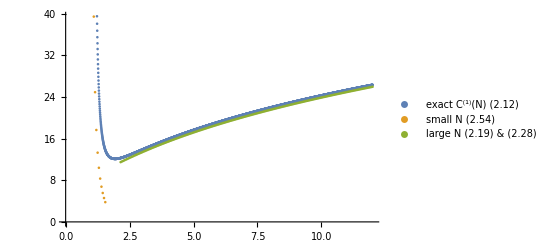

```mathematica
ListPlot[{tableExact, tableNsmall, tableNlarge}, PlotLegends -> {"exact C^(1)(N) (2.12)", "small N (2.54)", "large N (2.19) & (2.28)"}]
```